{9.62,9.9,4.25,11.51,13.45,12.47,18.26,4.98,12.46,13.62,14.74,4.08,11.17,9.11,9.58,17.2,8.42,15.46,9.91,12.59,11.73,1.2,15.12,13.08,17.32,13.84,20.76,11.95,12.47,13.02,19.05,13.41,16.91,13.2,13.13,11.78,14.23,19.1,1.7,14.27,13.62,12.19,16.57,0.83,9.73,16.59,15.78,12.26,13.93,10.94,15.15,10.25,14.26,13.79,15.82,11.11,15.,12.85,11.4,13.36,17.54,9.78,15.05,9.16,15.97,4.46,14.27,20.18,11.91,13.18,10.78,15.,11.73,9.16,12.2,13.76,14.71,0.25,8.01,16.93,12.56,9.81,11.53,10.19,17.3,13.41,14.87,13.21,12.95,10.65,9.25,8.89,14.89,18.84,13.45,11.95,10.95,18.67,4.36,10.22}

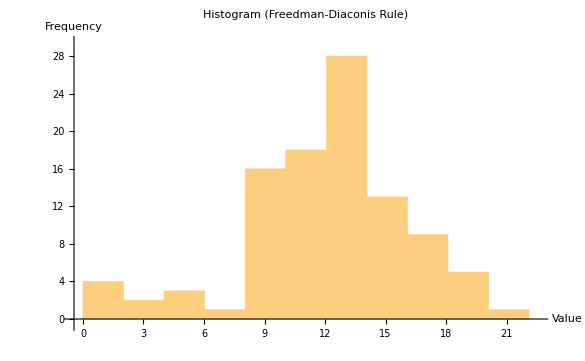

Sample Size (n): 100

Interquartile Range (IQR): 4.645

Bin Width (h): 2.01

Number of Bins: 11

Bins: {{0.25,2.26},{2.26,4.27},{4.27,6.28},{6.28,8.29},{8.29,10.3},{10.3,12.31},{12.31,14.32},{14.32,16.33},{16.33,18.34},{18.34,20.35},{20.35,22.36}}

Counts: {4,2,3,1,16,18,28,13,9,5,1}

IQR: 4.645

```mathematica
data={9.62,9.90,4.25,11.51,13.45,12.47,18.26,4.98,12.46,13.62,14.74,4.08,11.17,9.11,9.58,17.20,8.42,15.46,9.91,12.59,11.73,1.20,15.12,13.08,17.32,13.84,20.76,11.95,12.47,13.02,19.05,13.41,16.91,13.2,13.13,11.78,14.23,19.10,1.70,14.27,13.62,12.19,16.57,0.83,9.73,16.59,15.78,12.26,13.93,10.94,15.15,10.25,14.26,13.79,15.82,11.11,15.00,12.85,11.40,13.36,17.54,9.78,15.05,9.16,15.97,4.46,14.27,20.18,11.91,13.18,10.78,15.00,11.73,9.16,12.20,13.76,14.71,0.25,8.01,16.93,12.56,9.81,11.53,10.19,17.30,13.41,14.87,13.21,12.95,10.65,9.25,8.89,14.89,18.84,13.45,11.95,10.95,18.67,4.36,10.22}  (*或者替换成你自己的数据*)

(*计算样本大小*)
n=Length[data];

(*计算四分位距 (IQR)*)
iqr=InterquartileRange[data];

(*计算 bin 宽度 (h) 根据 Freedman-Diaconis 规则*)
h=Ceiling[2*iqr/(n^(1/3)),0.01];

(*确定 bin 的数量*)
dataMin=Min[data];
dataMax=Max[data];
numBins=Ceiling[(dataMax-dataMin)/h];

(*创建 bins*)
bins=Table[{dataMin+(i-1)*h,dataMin+i*h},{i,1,numBins}];

(*统计每个 bin 中的数据点数量*)
counts=Table[Count[data,x_/;bins[[i,1]]<=x<bins[[i,2]]],{i,1,numBins}];

(*处理最后一个 bin,包含右端点*)
counts[[numBins]]=Count[data,x_/;bins[[numBins,1]]<=x<=bins[[numBins,2]]];


(*创建 Histogram 数据格式*)
histogramData=Table[{Mean[bins[[i]]],counts[[i]]},{i,1,numBins}];

(*绘制 Histogram*)
Histogram[Flatten[Table[ConstantArray[histogramData[[i,1]],histogramData[[i,2]]],{i,Length[histogramData]}]],{h},ChartLabels->Automatic,AxesLabel->{"Value","Frequency"},PlotLabel->"Histogram (Freedman-Diaconis Rule)",ImageSize->Large,PlotRange->All]
Print["Sample Size (n): ",n];
Print["Interquartile Range (IQR): ",iqr];
Print["Bin Width (h): ",h];
Print["Number of Bins: ",numBins];
Print["Bins: ",bins];
Print["Counts: ",counts];
Print["IQR: ",iqr];
```